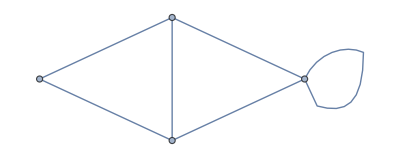
{-Graphics-,-Graphics-}

```mathematica
{WeightedAdjacencyGraph[({{1, 1, 2, ∞}, {1, ∞, 1, 1}, {2, 1, ∞, 3}, {∞, 1, 3, ∞}})],WeightedAdjacencyGraph[({{∞, 2, ∞, ∞}, {1, ∞, ∞, ∞}, {1, 1, 1, ∞}, {3, 1, ∞, ∞}})]}
```

```mathematica
First[{WeightedAdjacencyGraph[({{1, 1, 2, ∞}, {1, ∞, 1, 1}, {2, 1, ∞, 3}, {∞, 1, 3, ∞}})],WeightedAdjacencyGraph[({{∞, 2, ∞, ∞}, {1, ∞, ∞, ∞}, {1, 1, 1, ∞}, {3, 1, ∞, ∞}})]}]
```

-Graphics-

```mathematica
WeightedAdjacencyMatrix[First[{WeightedAdjacencyGraph[({{1, 1, 2, ∞}, {1, ∞, 1, 1}, {2, 1, ∞, 3}, {∞, 1, 3, ∞}})],WeightedAdjacencyGraph[({{∞, 2, ∞, ∞}, {1, ∞, ∞, ∞}, {1, 1, 1, ∞}, {3, 1, ∞, ∞}})]}]]//Normal//MatrixForm
```

(1 | 1 | 2 | 0
1 | 0 | 1 | 1
2 | 1 | 0 | 3
0 | 1 | 3 | 0)

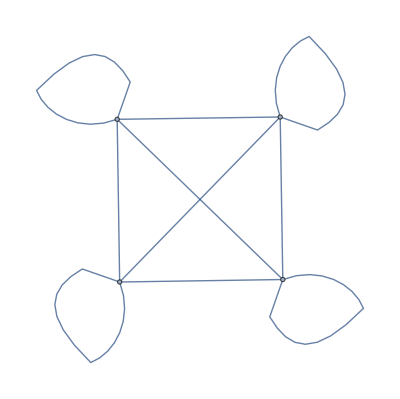

```mathematica
WeightedAdjacencyGraph[Normal@WeightedAdjacencyMatrix[First[{WeightedAdjacencyGraph[({{1, 1, 2, ∞}, {1, ∞, 1, 1}, {2, 1, ∞, 3}, {∞, 1, 3, ∞}})],WeightedAdjacencyGraph[({{∞, 2, ∞, ∞}, {1, ∞, ∞, ∞}, {1, 1, 1, ∞}, {3, 1, ∞, ∞}})]}]]]
```

```mathematica
WeightedAdjacencyGraph@ReplaceAll[Normal@WeightedAdjacencyMatrix[First[{WeightedAdjacencyGraph[({{1, 1, 2, ∞}, {1, ∞, 1, 1}, {2, 1, ∞, 3}, {∞, 1, 3, ∞}})],WeightedAdjacencyGraph[({{∞, 2, ∞, ∞}, {1, ∞, ∞, ∞}, {1, 1, 1, ∞}, {3, 1, ∞, ∞}})]}]],0->∞]
```

-Graphics-